```mathematica
-Graphics-;
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<mathutils.m;
(*<<ed5314utils_en.m;*)
<<kinematic_utils.m
<<MaTeX`
```

e1, e2, e3  are Rodrigues parameters:

```mathematica
phi={e1,e2,e3};
```

```mathematica
phimat={{0,-e3,e2},{e3,0,-e1},{-e2,e1,0}};
```

```mathematica
phimat//MatrixForm
```

(0 | -e3 | e2
e3 | 0 | -e1
-e2 | e1 | 0)

```mathematica
Rphi=Simplify[IdentityMatrix[3]+2*(((phimat)+(phimat.phimat))/(1+e1^2+e2^2+e3^2))]
```

{{1-(2 (e2^2+e3^2))/(1+e1^2+e2^2+e3^2),(2 e1 e2-2 e3)/(1+e1^2+e2^2+e3^2),(2 (e2+e1 e3))/(1+e1^2+e2^2+e3^2)},{(2 (e1 e2+e3))/(1+e1^2+e2^2+e3^2),1-(2 (e1^2+e3^2))/(1+e1^2+e2^2+e3^2),-(2 (e1-e2 e3))/(1+e1^2+e2^2+e3^2)},{(2 (-e2+e1 e3))/(1+e1^2+e2^2+e3^2),(2 (e1+e2 e3))/(1+e1^2+e2^2+e3^2),1-(2 (e1^2+e2^2))/(1+e1^2+e2^2+e3^2)}}

```mathematica
Simplify[Rphi.Transpose[Rphi]]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
A1={0,0,0};
A2={a2x,a2y,a2z};
A3={a3x,a3y,a3z};
```

```mathematica
b1d={b1x,b1y,b1z};
b2d={b2x,b2y,b2z};
b3d={b3x,b3y,b3z};
```

```mathematica
X={x,y,z};
```

```mathematica
r1=Rphi.b1d;
r2=Rphi.b2d;
r3=Rphi.b3d;
```

```mathematica
B1=X+r1;
B2=X+r2;
B3=X+r3;
```

```mathematica
s1=B1-A1;
s2=B2-A2;
s3=B3-A3;
```

```mathematica
n1=(({s1}.Transpose[{s1}])[[1,1]])-ρ1^2;
n2=(({s2}.Transpose[{s2}])[[1,1]])-ρ2^2;
n3=(({s3}.Transpose[{s3}])[[1,1]])-ρ3^2;
```

```mathematica
q1=Expand[Together[n1]*(1+e1^2+e2^2+e3^2)]
```

b1x^2+b1y^2+b1z^2+b1x^2 e1^2+b1y^2 e1^2+b1z^2 e1^2+b1x^2 e2^2+b1y^2 e2^2+b1z^2 e2^2+b1x^2 e3^2+b1y^2 e3^2+b1z^2 e3^2+2 b1x x+2 b1x e1^2 x+4 b1z e2 x+4 b1y e1 e2 x-2 b1x e2^2 x-4 b1y e3 x+4 b1z e1 e3 x-2 b1x e3^2 x+x^2+e1^2 x^2+e2^2 x^2+e3^2 x^2+2 b1y y-4 b1z e1 y-2 b1y e1^2 y+4 b1x e1 e2 y+2 b1y e2^2 y+4 b1x e3 y+4 b1z e2 e3 y-2 b1y e3^2 y+y^2+e1^2 y^2+e2^2 y^2+e3^2 y^2+2 b1z z+4 b1y e1 z-2 b1z e1^2 z-4 b1x e2 z-2 b1z e2^2 z+4 b1x e1 e3 z+4 b1y e2 e3 z+2 b1z e3^2 z+z^2+e1^2 z^2+e2^2 z^2+e3^2 z^2-ρ1^2-e1^2 ρ1^2-e2^2 ρ1^2-e3^2 ρ1^2

```mathematica
q2=Expand[Together[n2-n1]*(1+e1^2+e2^2+e3^2)]
```

a2x^2+a2y^2+a2z^2-b1x^2-b1y^2-b1z^2-2 a2x b2x+b2x^2-2 a2y b2y+b2y^2-2 a2z b2z+b2z^2-4 a2z b2y e1+4 a2y b2z e1+a2x^2 e1^2+a2y^2 e1^2+a2z^2 e1^2-b1x^2 e1^2-b1y^2 e1^2-b1z^2 e1^2-2 a2x b2x e1^2+b2x^2 e1^2+2 a2y b2y e1^2+b2y^2 e1^2+2 a2z b2z e1^2+b2z^2 e1^2+4 a2z b2x e2-4 a2x b2z e2-4 a2y b2x e1 e2-4 a2x b2y e1 e2+a2x^2 e2^2+a2y^2 e2^2+a2z^2 e2^2-b1x^2 e2^2-b1y^2 e2^2-b1z^2 e2^2+2 a2x b2x e2^2+b2x^2 e2^2-2 a2y b2y e2^2+b2y^2 e2^2+2 a2z b2z e2^2+b2z^2 e2^2-4 a2y b2x e3+4 a2x b2y e3-4 a2z b2x e1 e3-4 a2x b2z e1 e3-4 a2z b2y e2 e3-4 a2y b2z e2 e3+a2x^2 e3^2+a2y^2 e3^2+a2z^2 e3^2-b1x^2 e3^2-b1y^2 e3^2-b1z^2 e3^2+2 a2x b2x e3^2+b2x^2 e3^2+2 a2y b2y e3^2+b2y^2 e3^2-2 a2z b2z e3^2+b2z^2 e3^2-2 a2x x-2 b1x x+2 b2x x-2 a2x e1^2 x-2 b1x e1^2 x+2 b2x e1^2 x-4 b1z e2 x+4 b2z e2 x-4 b1y e1 e2 x+4 b2y e1 e2 x-2 a2x e2^2 x+2 b1x e2^2 x-2 b2x e2^2 x+4 b1y e3 x-4 b2y e3 x-4 b1z e1 e3 x+4 b2z e1 e3 x-2 a2x e3^2 x+2 b1x e3^2 x-2 b2x e3^2 x-2 a2y y-2 b1y y+2 b2y y+4 b1z e1 y-4 b2z e1 y-2 a2y e1^2 y+2 b1y e1^2 y-2 b2y e1^2 y-4 b1x e1 e2 y+4 b2x e1 e2 y-2 a2y e2^2 y-2 b1y e2^2 y+2 b2y e2^2 y-4 b1x e3 y+4 b2x e3 y-4 b1z e2 e3 y+4 b2z e2 e3 y-2 a2y e3^2 y+2 b1y e3^2 y-2 b2y e3^2 y-2 a2z z-2 b1z z+2 b2z z-4 b1y e1 z+4 b2y e1 z-2 a2z e1^2 z+2 b1z e1^2 z-2 b2z e1^2 z+4 b1x e2 z-4 b2x e2 z-2 a2z e2^2 z+2 b1z e2^2 z-2 b2z e2^2 z-4 b1x e1 e3 z+4 b2x e1 e3 z-4 b1y e2 e3 z+4 b2y e2 e3 z-2 a2z e3^2 z-2 b1z e3^2 z+2 b2z e3^2 z+ρ1^2+e1^2 ρ1^2+e2^2 ρ1^2+e3^2 ρ1^2-ρ2^2-e1^2 ρ2^2-e2^2 ρ2^2-e3^2 ρ2^2

```mathematica
q3=Expand[Together[n3-n1]*(1+e1^2+e2^2+e3^2)]
```

a3x^2+a3y^2+a3z^2-b1x^2-b1y^2-b1z^2-2 a3x b3x+b3x^2-2 a3y b3y+b3y^2-2 a3z b3z+b3z^2-4 a3z b3y e1+4 a3y b3z e1+a3x^2 e1^2+a3y^2 e1^2+a3z^2 e1^2-b1x^2 e1^2-b1y^2 e1^2-b1z^2 e1^2-2 a3x b3x e1^2+b3x^2 e1^2+2 a3y b3y e1^2+b3y^2 e1^2+2 a3z b3z e1^2+b3z^2 e1^2+4 a3z b3x e2-4 a3x b3z e2-4 a3y b3x e1 e2-4 a3x b3y e1 e2+a3x^2 e2^2+a3y^2 e2^2+a3z^2 e2^2-b1x^2 e2^2-b1y^2 e2^2-b1z^2 e2^2+2 a3x b3x e2^2+b3x^2 e2^2-2 a3y b3y e2^2+b3y^2 e2^2+2 a3z b3z e2^2+b3z^2 e2^2-4 a3y b3x e3+4 a3x b3y e3-4 a3z b3x e1 e3-4 a3x b3z e1 e3-4 a3z b3y e2 e3-4 a3y b3z e2 e3+a3x^2 e3^2+a3y^2 e3^2+a3z^2 e3^2-b1x^2 e3^2-b1y^2 e3^2-b1z^2 e3^2+2 a3x b3x e3^2+b3x^2 e3^2+2 a3y b3y e3^2+b3y^2 e3^2-2 a3z b3z e3^2+b3z^2 e3^2-2 a3x x-2 b1x x+2 b3x x-2 a3x e1^2 x-2 b1x e1^2 x+2 b3x e1^2 x-4 b1z e2 x+4 b3z e2 x-4 b1y e1 e2 x+4 b3y e1 e2 x-2 a3x e2^2 x+2 b1x e2^2 x-2 b3x e2^2 x+4 b1y e3 x-4 b3y e3 x-4 b1z e1 e3 x+4 b3z e1 e3 x-2 a3x e3^2 x+2 b1x e3^2 x-2 b3x e3^2 x-2 a3y y-2 b1y y+2 b3y y+4 b1z e1 y-4 b3z e1 y-2 a3y e1^2 y+2 b1y e1^2 y-2 b3y e1^2 y-4 b1x e1 e2 y+4 b3x e1 e2 y-2 a3y e2^2 y-2 b1y e2^2 y+2 b3y e2^2 y-4 b1x e3 y+4 b3x e3 y-4 b1z e2 e3 y+4 b3z e2 e3 y-2 a3y e3^2 y+2 b1y e3^2 y-2 b3y e3^2 y-2 a3z z-2 b1z z+2 b3z z-4 b1y e1 z+4 b3y e1 z-2 a3z e1^2 z+2 b1z e1^2 z-2 b3z e1^2 z+4 b1x e2 z-4 b3x e2 z-2 a3z e2^2 z+2 b1z e2^2 z-2 b3z e2^2 z-4 b1x e1 e3 z+4 b3x e1 e3 z-4 b1y e2 e3 z+4 b3y e2 e3 z-2 a3z e3^2 z-2 b1z e3^2 z+2 b3z e3^2 z+ρ1^2+e1^2 ρ1^2+e2^2 ρ1^2+e3^2 ρ1^2-ρ3^2-e1^2 ρ3^2-e2^2 ρ3^2-e3^2 ρ3^2

```mathematica
te=q3;
{Exponent[te, x], Exponent[te, y], Exponent[te, z], Exponent[te, e1], Exponent[te, e2], Exponent[te, e3]}
```

{1,1,1,2,2,2}

```mathematica
(*These give 3 equations in 6 variables. We need 3 more equations in only these 6 variables to be able to solve it*)
```

```mathematica
monopoly[q3,{e1,e2,e3,x,y,z}]
```

{{a3x^2+a3y^2+a3z^2-b1x^2-b1y^2-b1z^2-2 a3x b3x+b3x^2-2 a3y b3y+b3y^2-2 a3z b3z+b3z^2+ρ1^2-ρ3^2,-2 a3z-2 b1z+2 b3z,-2 a3y-2 b1y+2 b3y,-2 a3x-2 b1x+2 b3x,-4 a3y b3x+4 a3x b3y,-4 b1x+4 b3x,4 b1y-4 b3y,a3x^2+a3y^2+a3z^2-b1x^2-b1y^2-b1z^2+2 a3x b3x+b3x^2+2 a3y b3y+b3y^2-2 a3z b3z+b3z^2+ρ1^2-ρ3^2,-2 a3z-2 b1z+2 b3z,-2 a3y+2 b1y-2 b3y,-2 a3x+2 b1x-2 b3x,4 a3z b3x-4 a3x b3z,4 b1x-4 b3x,-4 b1z+4 b3z,-4 a3z b3y-4 a3y b3z,-4 b1y+4 b3y,-4 b1z+4 b3z,a3x^2+a3y^2+a3z^2-b1x^2-b1y^2-b1z^2+2 a3x b3x+b3x^2-2 a3y b3y+b3y^2+2 a3z b3z+b3z^2+ρ1^2-ρ3^2,-2 a3z+2 b1z-2 b3z,-2 a3y-2 b1y+2 b3y,-2 a3x+2 b1x-2 b3x,-4 a3z b3y+4 a3y b3z,-4 b1y+4 b3y,4 b1z-4 b3z,-4 a3z b3x-4 a3x b3z,-4 b1x+4 b3x,-4 b1z+4 b3z,-4 a3y b3x-4 a3x b3y,-4 b1x+4 b3x,-4 b1y+4 b3y,a3x^2+a3y^2+a3z^2-b1x^2-b1y^2-b1z^2-2 a3x b3x+b3x^2+2 a3y b3y+b3y^2+2 a3z b3z+b3z^2+ρ1^2-ρ3^2,-2 a3z+2 b1z-2 b3z,-2 a3y+2 b1y-2 b3y,-2 a3x-2 b1x+2 b3x},{1,z,y,x,e3,e3 y,e3 x,e3^2,e3^2 z,e3^2 y,e3^2 x,e2,e2 z,e2 x,e2 e3,e2 e3 z,e2 e3 y,e2^2,e2^2 z,e2^2 y,e2^2 x,e1,e1 z,e1 y,e1 e3,e1 e3 z,e1 e3 x,e1 e2,e1 e2 y,e1 e2 x,e1^2,e1^2 z,e1^2 y,e1^2 x}}

```mathematica
II={1,0,0};
JJ={0,1,0};
KK={0,0,1};
```

```mathematica
G0=X-KK;
```

```mathematica
Zero31={0,0,0};
```

```mathematica
Mo=Join[(Join[Transpose[{-s1}],Transpose[{-s2}],Transpose[{-s3}],Transpose[{KK}],2]),(Join[Transpose[{Zero31}],Transpose[{Cross[-A2,s2]}],Transpose[{Cross[-A3,s3]}],Transpose[{Cross[X,KK]}],2])];
```

```mathematica
MA2=Join[(Join[Transpose[{-s1}],Transpose[{-s2}],Transpose[{-s3}],Transpose[{KK}],2]),(Join[Transpose[{Cross[-(A1-A2),s1]}],Transpose[{Zero31}],Transpose[{Cross[-(A3-A2),s3]}],Transpose[{Cross[(X-A2),KK]}],2])];
```

```mathematica
MA3=Join[(Join[Transpose[{-s1}],Transpose[{-s2}],Transpose[{-s3}],Transpose[{KK}],2]),(Join[Transpose[{Cross[-(A1-A3),s1]}],Transpose[{Cross[-(A2-A3),s2]}],Transpose[{Zero31}],Transpose[{Cross[(X-A3),KK]}],2])];
```

```mathematica
MB1=Join[(Join[Transpose[{-s1}],Transpose[{-s2}],Transpose[{-s3}],Transpose[{KK}],2]),(Join[Transpose[{Zero31}],Transpose[{Cross[-(A2-B1),s2]}],Transpose[{Cross[-(A3-B1),s3]}],Transpose[{Cross[(X-B1),KK]}],2])];
```

```mathematica
MB2=Join[(Join[Transpose[{-s1}],Transpose[{-s2}],Transpose[{-s3}],Transpose[{KK}],2]),(Join[Transpose[{Cross[-(A1-B2),s1]}],Transpose[{Zero31}],Transpose[{Cross[-(A3-B2),s3]}],Transpose[{Cross[(X-B2),KK]}],2])];
```

```mathematica
MB3=Join[(Join[Transpose[{-s1}],Transpose[{-s2}],Transpose[{-s3}],Transpose[{KK}],2]),(Join[Transpose[{Cross[-(A1-B3),s1]}],Transpose[{Cross[-(A2-B3),s2]}],Transpose[{Zero31}],Transpose[{Cross[(X-B3),KK]}],2])];
```

```mathematica
MG=Join[(Join[Transpose[{-s1}],Transpose[{-s2}],Transpose[{-s3}],Transpose[{KK}],2]),(Join[Transpose[{Cross[-(A1-X),s1]}],Transpose[{Cross[-(A2-X),s2]}],Transpose[{Cross[-(A3-X),s3]}],Transpose[{Cross[(X-X),KK]}],2])];
```

```mathematica
MG0=Join[(Join[Transpose[{-s1}],Transpose[{-s2}],Transpose[{-s3}],Transpose[{KK}],2]),(Join[Transpose[{Cross[-(A1-G0),s1]}],Transpose[{Cross[-(A2-G0),s2]}],Transpose[{Cross[-(A3-G0),s3]}],Transpose[{Cross[(X-G0),KK]}],2])];
```

```mathematica
MG0//Dimensions
```

{6,4}

```mathematica
p1=Expand[Together[Det[Join[Mo[[1;;3,1;;4]],Mo[[6;;6,1;;4]]]]]*((1+e1^2+e2^2+e3^2)^2)];
p2=Expand[Together[Det[Join[Mo[[1;;3,1;;4]],Mo[[5;;5,1;;4]]]]]*((1+e1^2+e2^2+e3^2)^2)];
p3=Expand[Together[Det[Join[Mo[[1;;3,1;;4]],Mo[[4;;4,1;;4]]]]]*((1+e1^2+e2^2+e3^2)^2)];
```

```mathematica
p4=Expand[Together[Det[Mo[[4;;6,2;;4]]]]*((1+e1^2+e2^2+e3^2)^2)];
```

```mathematica
p5=Expand[Together[Det[MB1[[4;;6,2;;4]]]]*((1+e1^2+e2^2+e3^2)^2)];
p6=Expand[Together[Det[Join[MB2[[4;;6,1;;1]],MB2[[4;;6,3;;4]],2]]]*((1+e1^2+e2^2+e3^2)^2)];
p7=Expand[Together[Det[Join[MA2[[4;;6,1;;1]],MA2[[4;;6,3;;4]],2]]]*((1+e1^2+e2^2+e3^2)^2)];
p8=Expand[Together[Det[Join[MB3[[4;;6,1;;2]],MB3[[4;;6,4;;4]],2]]]*((1+e1^2+e2^2+e3^2)^2)];
p9=Expand[Together[Det[Join[MA3[[4;;6,1;;2]],MA3[[4;;6,4;;4]],2]]]*((1+e1^2+e2^2+e3^2)^2)];
p10=Expand[Together[Det[MG[[4;;6,1;;3]]]]*((1+e1^2+e2^2+e3^2)^2)];
```

```mathematica
p11=Expand[Together[Det[MG0[[4;;6,1;;3]]]]*((1+e1^2+e2^2+e3^2)^2)];
```

```mathematica
monopoly[p11,{e3,x,y,z}][[2]]
```

{1,z,z^2,y,y z,y^2,x,x z,x y,x^2,e3,e3 z,e3 z^2,e3 y,e3 y z,e3 y^2,e3 x,e3 x z,e3 x y,e3 x^2,e3^2,e3^2 z,e3^2 z^2,e3^2 y,e3^2 y z,e3^2 y^2,e3^2 x,e3^2 x z,e3^2 x y,e3^2 x^2,e3^3,e3^3 z,e3^3 z^2,e3^3 y,e3^3 y z,e3^3 y^2,e3^3 x,e3^3 x z,e3^3 x y,e3^3 x^2,e3^4,e3^4 z,e3^4 z^2,e3^4 y,e3^4 y z,e3^4 y^2,e3^4 x,e3^4 x z,e3^4 x y,e3^4 x^2}

```mathematica
basedata={a2x-> 10,a2y-> 0,a2z-> 0,a3x-> 0,a3y-> 12,a3z-> 0};
platformdata={b1x-> 1,b1y-> 0,b1z-> 0,b2x-> 0,b2y-> 1,b2z-> 0,b3x-> 0,b3y-> 0,b3z-> 1};
cablelendata={ρ1-> 75/10,ρ2-> 10,ρ3-> 95/10};
numdata=Union[basedata,platformdata,cablelendata];
```

```mathematica
numdata
```

{a2x→10,a2y→0,a2z→0,a3x→0,a3y→12,a3z→0,b1x→1,b1y→0,b1z→0,b2x→0,b2y→1,b2z→0,b3x→0,b3y→0,b3z→1,ρ1→15/2,ρ2→10,ρ3→19/2}

```mathematica
numdata2 = Union[basedata,platformdata]
```

{a2x→10,a2y→0,a2z→0,a3x→0,a3y→12,a3z→0,b1x→1,b1y→0,b1z→0,b2x→0,b2y→1,b2z→0,b3x→0,b3y→0,b3z→1}

```mathematica
q1n=q1/.numdata;
q2n=q2/.numdata;
q3n=q3/.numdata;
p1n=p1/.numdata;
p2n=p2/.numdata;p3n=p3/.numdata;p4n=p4/.numdata;p5n=p5/.numdata;p6n=p6/.numdata;p7n=p7/.numdata;p8n=p8/.numdata;p9n=p9/.numdata;p10n=p10/.numdata;p11n=p11/.numdata;
```

```mathematica
polys1={q1n,q2n,q3n,p1n,p2n,p3n,p4n,p5n,p6n,p7n,p8n,p9n,p10n,p11n};
```

```mathematica
ByteCount[polys1]/1024//N
```

270.742

```mathematica
polys1//Variables
```

{e1,e2,e3,x,y,z}

```mathematica
polys1//Dimensions
```

{14}

```mathematica
(*We have in total of 14 equations in 6 variables.*)
```

```mathematica
(*Since we only need 6 equations for the 6 variables and also it is given that the obtained solutions are linearly independent but are nolinearly dependent. Assuming that this means that these might have additional terms multiplying the equations and hence selecting the lowest degree polynomials to obtain the FK solutions. We'll need to check if we cover all the solutions with this choice of polynomials*)
```

```mathematica
(*Working with p1, p2, p3 and q1, q2, q3*)
```

```mathematica
eqns = {q1n, q2n, q3n, p1n, p2n, p3n};
```

```mathematica
eqns//Variables
```

{e1,e2,e3,x,y,z}

```mathematica
eqns//Dimensions
```

{6}

```mathematica
(*Now we have 6 equations in 6 variables. But since it is underconstrained should something else be added? Assumption is that: Since we took equations from both geometric conditions and the statics, these solutions are definitely feasible, but 1. Needs to checked with the other polynomials to see if they also satisfy these solutions, 2. See if we obtain an additional set of unique solutions if a set of any other 3 equations are taken and verify that all the equations satisfy its. After this it should also be checked if the solutions have +ve tension. Or after one round of computation, take the tensions also as variables to be computed and use the 9 equations to solve for both x, y, z, e1, e2, e3, τ1, τ2, τ3 together*)
```

```mathematica
(*Starting with a reported FK solution*)
```

```mathematica
init = {-4.2220, -5.9042, -0.4719, 1.6805, 3.5743, 5.5605};
vars = {e1,e2,e3,x,y,z};
```

```mathematica
ambrule = Chop[{e3->-1.247955093239938+0. ⅈ,e2->2.590308940304512+0. ⅈ,e1->-0.5044737495492316+0. ⅈ,x->3.5231340130208024+0. ⅈ,y->5.532023321262042+0. ⅈ,z->5.2626779174487455+0. ⅈ}]
```

{e3→-1.24796,e2→2.59031,e1→-0.504474,x→3.52313,y→5.53202,z→5.26268}

```mathematica
initrule = Inner[Rule, vars, init, List]
```

{e1→-4.222,e2→-5.9042,e3→-0.4719,x→1.6805,y→3.5743,z→5.5605}

```mathematica
eqns/.ambrule
```

{-0.0000634339,0.0000372728,0.000105553,-0.00646903,0.00535289,0.000992899}

```mathematica
polys1/.ambrule
```

{-0.0000634339,0.0000372728,0.000105553,-0.00646903,0.00535289,0.000992899,-0.00876416,-0.00153018,0.000353735,-0.011662,-0.000224646,0.0583136,-0.00162925,-0.00238882}

```mathematica
q1n2=q1/.numdata2;
q2n2=q2/.numdata2;
q3n2=q3/.numdata2;
p1n2=p1/.numdata2;
p2n2=p2/.numdata2;
p3n2=p3/.numdata2;
p4n2=p4/.numdata2;
p5n2=p5/.numdata2;
p6n2=p6/.numdata2;
p7n2=p7/.numdata2;
p8n2=p8/.numdata2;
p9n2=p9/.numdata2;
```

```mathematica
η = {q1n2, q2n2, q3n2, p1n2, p2n2, p3n2};
Variables[η]
```

{e1,e2,e3,x,y,z,ρ1,ρ2,ρ3}

```mathematica
η//Variables
```

{e1,e2,e3,x,y,z,ρ1,ρ2,ρ3}

```mathematica
(*file=Import["CDPRC.txt","Text"]*)
```

```mathematica
cη = Compile[{{e1, _Real},{e2, _Real},{e3, _Real},{x, _Real},{y, _Real}, {z, _Real}, {ρ1, _Real}, {ρ2, _Real}, {ρ3, _Real}}, Evaluate[η], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
sym2 = {ρ1->rh1, ρ2->rh2, ρ3->rh3};
```

#### Numerical substitution rules:

```mathematica
inversetrig = Union[{ArcTan[x_, y_]->atan2[y,x]} , {ArcCos[x_]->acos[x]}];
trigrules =  Union[{Sin[x_]-> sin[x]},{Cos[x_]-> cos[x]},{Tan[x_]-> tan[x]},{Csc[x_]-> 1/sin[x]},{Sec[x_]-> 1/cos[x]},{Cot[x_]->sin[x]/cos[x]}];
(*Rules for removing the greek symbols*)
phi = Table[Symbol["p"<>ToString[i]],{i, 6}];
psi = Table[Symbol["s"<>ToString[i]],{i, 6}];
dphi = Table[Symbol["dp"<>ToString[i]],{i, 6}];
dpsi = Table[Symbol["ds"<>ToString[i]],{i, 6}];
nogreek = Join[Inner[Rule, ϕ, phi, List], Inner[Rule, ψ, psi, List], Inner[Rule, dϕ, dphi, List], Inner[Rule, dψ, dpsi, List]];
(*Replacing all the cos, sin[ϕ's] and cos, sin[ψ's]*)
cospsi = Table[Symbol["cs"<>ToString[i]],{i, 6}];
sinpsi = Table[Symbol["ss"<>ToString[i]],{i, 6}];
cosphi = Table[Symbol["cp"<>ToString[i]],{i, 6}];
sinphi = Table[Symbol["sp"<>ToString[i]],{i, 6}];
(*Most of the expressions have repeated sin and cosine which needs to be computed only once*)
trigtoalg = Join[Inner[Rule, Cos[ψ], cospsi, List], Inner[Rule, Sin[ψ], sinpsi, List], Inner[Rule, Cos[ϕ], cosphi, List], Inner[Rule, Sin[ϕ], sinphi, List]];
replist=Union[{Power-> pow}, inversetrig, trigtoalg, nogreek];
```

Inner::normal: Nonatomic expression expected at position 2 in Inner[Rule,ϕ,{-a2y a3y b1x b2x+a2y a3x b1y b2x+a2x a3y b1x b2y-a2x a3x b1y b2y+a2y a3y b1x b3x-a2x a3y b1y b3x-a2y b1y b2x b3x+«55»+2 a2x b1x b2y b3y e1^2-2 a3x b1x b2y b3y e1^2+4 a2x a3x b1z b3z e1^2-4 a3x b1z b2x b3z e1^2-4 a2x b1x b2z b3z e1^2+4 a3x b1x b2z b3z e1^2+«2454»,«4»,-a3z b1y b2x b2y b3x+«75»},List].

Inner::normal: Nonatomic expression expected at position 2 in Inner[Rule,ψ,{{(b1y (2 e1 e2-2 e3))/(1+Power[«2»]+Power[«2»]+Power[«2»])+(2 b1z (e2+e1 e3))/(1+Power[«2»]+Power[«2»]+Power[«2»])+b1x (1-2 Plus[«2»] Power[«2»])+x,«4»+y,(2 b1x (-e2+e1 e3))/(1+Power[«2»]+Power[«2»]+Power[«2»])+(2 b1y (e1+e2 e3))/(1+Power[«2»]+Power[«2»]+Power[«2»])+b1z (1-2 Plus[«2»] Power[«2»])+z},«4»,s6},List].

Inner::normal: Nonatomic expression expected at position 2 in Inner[Rule,dϕ,{dp1,dp2,dp3,dp4,dp5,dp6},List].

General::stop: Further output of Inner::normal will be suppressed during this calculation.

Inner::argb: Inner called with 16 arguments; between 3 and 5 arguments are expected.

Inner::heads: Heads List and Cos at positions 3 and 2 are expected to be the same.

Inner::heads: Heads List and Sin at positions 3 and 2 are expected to be the same.

Inner::heads: Heads List and Cos at positions 3 and 2 are expected to be the same.

General::stop: Further output of Inner::heads will be suppressed during this calculation.

Inner::argb: Inner called with 16 arguments; between 3 and 5 arguments are expected.

Union::heads: Heads Inner and List at positions 3 and 1 are expected to be the same.

```mathematica
ηc = Table[ToString[CForm[η[[i]]/.sym2]/.Power->pow],{i, Length[η]}];
```

```mathematica
Jn = D[η, {vars}];
Jn//Variables
```

{e1,e2,e3,x,y,z,ρ1,ρ2,ρ3}

```mathematica
Jη = Table[ToString[CForm[Flatten[Jn/.sym2][[i]]]/.Power->pow],{i, Length[Flatten[Jn]]}];
```

```mathematica
(*FileTemplateApply[file,<|"text"->Evaluate[ηc], "text2"->Evaluate[Jη]|>,"CDPRC_out.txt"]*)
```

```mathematica
cη@@Join[(vars/.ambrule), {ρ1, ρ2, ρ3}/.cablelendata]
```

{-0.0000634339,0.0000372728,0.000105553,-0.00646903,0.00535289,0.000992899}

```mathematica
cJn = Compile[{{e1, _Real},{e2, _Real},{e3, _Real},{x, _Real},{y, _Real}, {z, _Real}, {ρ1, _Real}, {ρ2, _Real}, {ρ3, _Real}}, Evaluate[Jn], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
cJn@@Join[(vars/.ambrule), {ρ1, ρ2, ρ3}/.cablelendata]
```

{{8.33906,11.3825,-9.49519,53.0665,95.1285,92.3751},{-44.4937,39.2052,114.428,-176.642,22.0144,-7.10526},{17.9379,-57.3858,-72.663,26.9047,-229.212,-0.970611},{20601.8,3305.29,-2288.27,7929.12,2307.66,0.},{-8330.58,-2546.88,-15874.5,-3535.52,-6054.78,-1667.35},{4226.25,-6626.66,777.232,8318.58,2159.15,-1260.83}}

```mathematica
Flatten[cJn@@Join[(vars/.ambrule), {ρ1, ρ2, ρ3}/.cablelendata]]
```

{8.33906,11.3825,-9.49519,53.0665,95.1285,92.3751,-44.4937,39.2052,114.428,-176.642,22.0144,-7.10526,17.9379,-57.3858,-72.663,26.9047,-229.212,-0.970611,20601.8,3305.29,-2288.27,7929.12,2307.66,0.,-8330.58,-2546.88,-15874.5,-3535.52,-6054.78,-1667.35,4226.25,-6626.66,777.232,8318.58,2159.15,-1260.83}

```mathematica
bla2 = (vars/.ambrule) - LinearSolve[cJn@@Join[(vars/.ambrule), {ρ1, ρ2, ρ3}/.cablelendata], cη@@Join[(vars/.ambrule), {ρ1, ρ2, ρ3}/.cablelendata]]
```

{-0.504474,2.59031,-1.24796,3.52313,5.53202,5.26268}

```mathematica
{ρ1, ρ2, ρ3}/.cablelendata
```

{15/2,10,19/2}

```mathematica
cη@@Join[bla2, {ρ1, ρ2, ρ3}/.cablelendata]
```

{3.05249×10^-11,-2.55511×10^-11,-4.19504×10^-11,5.88784×10^-9,-5.33555×10^-9,-2.57444×10^-10}

```mathematica
vars
```

{e1,e2,e3,x,y,z}

```mathematica
SetPrecision[bla2,20]
```

{-0.50447375811886008279,2.5903097146893223623,-1.2479550929595308872,3.5231344366007002478,5.5320236367501101071,5.262677941305753393}

```mathematica
Inner[Rule, vars, bla2, List]
```

{e1→-0.504474,e2→2.59031,e3→-1.24796,x→3.52313,y→5.53202,z→5.26268}

```mathematica
η[[1]]/.Inner[Rule, vars, bla2, List]/.ρ1->7.5
```

3.04681×10^-11

```mathematica
CForm[η[[1]]/.sym2]/.Power->pow
```

1 + 2*x + 4*e1*e2*y + 4*e3*y - 4*e2*z + 4*e1*e3*z + pow(e1,2) + 2*x*pow(e1,2) + 
   pow(e2,2) - 2*x*pow(e2,2) + pow(e3,2) - 2*x*pow(e3,2) - pow(rh1,2) - 
   pow(e1,2)*pow(rh1,2) - pow(e2,2)*pow(rh1,2) - pow(e3,2)*pow(rh1,2) + 
   pow(x,2) + pow(e1,2)*pow(x,2) + pow(e2,2)*pow(x,2) + pow(e3,2)*pow(x,2) + 
   pow(y,2) + pow(e1,2)*pow(y,2) + pow(e2,2)*pow(y,2) + pow(e3,2)*pow(y,2) + 
   pow(z,2) + pow(e1,2)*pow(z,2) + pow(e2,2)*pow(z,2) + pow(e3,2)*pow(z,2)

```mathematica
cablelendata
```

{ρ1→15/2,ρ2→10,ρ3→19/2}

```mathematica
η/.Inner[Rule, vars, bla2, List]/.cablelendata
```

{3.04681×10^-11,-2.55795×10^-11,-4.20641×10^-11,5.9008×10^-9,-5.31509×10^-9,-2.42835×10^-10}

```mathematica
bla2
```

{-0.504474,2.59031,-1.24796,3.52313,5.53202,5.26268}

```mathematica
LinearSolve[cJn@@Join[bla2, {ρ1, ρ2, ρ3}/.cablelendata], cη@@Join[bla2, {ρ1, ρ2, ρ3}/.cablelendata]]
```

{8.58113×10^-14,5.19908×10^-13,1.11022×10^-13,3.17019×10^-13,6.14829×10^-14,2.46144×10^-14}

```mathematica
TrackRoot[thetai_, phii_] :=  Module[{nvec, Jmat, δphi, loopcounter, tempphi},
nvec = cη@@Join[phii, thetai];
loopcounter=0;
tempphi = phii;
While[Max[Abs[nvec]]≥ 10^-10,
If[loopcounter≥ 100, Break];
loopcounter++;
Jmat =  cJn@@Join[tempphi, thetai];
δphi=LinearSolve[Jmat,nvec];
tempphi =tempphi-δphi;
nvec = cη@@Join[tempphi, thetai];
];
Return[tempphi];
]
```

```mathematica
(*7, 6, 5, *)
```

```mathematica
ambrule = Chop[{e3->1.711,e2->0.5425,e1->-3.3553,x->2.93,y->4.07,z->6.045}]
```

{e3→1.711,e2→0.5425,e1→-3.3553,x→2.93,y→4.07,z→6.045}

```mathematica
cη@@Join[vars/.ambrule, {ρ1, ρ2, ρ3}/.cablelendata]
```

{-1.04087,0.623874,2.48864,17.3079,-146.657,-33.9145}

```mathematica
{ρ1, ρ2, ρ3}/.cablelendata
```

{15/2,10,19/2}

```mathematica
test = TrackRoot[{ρ1, ρ2, ρ3}/.cablelendata, vars/.ambrule]
```

{-3.3554,0.542536,1.71102,2.93133,4.07689,6.04519}

```mathematica
test-vars/.ambrule
```

{-0.0000981638,0.0000359169,0.0000227662,0.00133317,0.00689036,0.000190574}

```mathematica
(*Confirming the NR solution*)
```

```mathematica
cη@@Join[test, {ρ1, ρ2, ρ3}/.cablelendata]
```

{-5.68434×10^-14,2.27374×10^-13,2.84217×10^-13,8.86757×10^-11,5.72982×10^-11,7.07701×10^-12}

```mathematica
(*Validating the solution for all the 15 equations*)
```

```mathematica
polys1/.Inner[Rule, vars, test, List]
```

{0.,3.41061×10^-13,2.27374×10^-13,2.91038×10^-11,5.09317×10^-11,2.18279×10^-11,-3.34694×10^-10,6.36646×10^-12,-3.18323×10^-12,-5.82077×10^-11,7.27596×10^-12,3.49246×10^-10,-1.45519×10^-11,3.27418×10^-11}

```mathematica
(*Doing root tracking by using the linear-interpolation of the lengths*)
```

```mathematica
rinitial = {15/2, 10, 19/2};
rfinal = {10,11,8};
rinter = Table[rinitial+ii*(rfinal-rinitial),{ii, 0, 1, 0.001}];
```

```mathematica
(*file = Import["rintervals.txt", "Text"]*)
```

```mathematica
(*FileTemplateApply[file,<|"vals"->Evaluate[Flatten[rinter]]|>,"rinterevals_out.txt"]*)
```

```mathematica
(*This gives the required poses*)
```

```mathematica
tic[]
tempϕ = test;
ϕlist = {tempϕ};
For[i=2,i≤Length[rinter], i++, 
tempϕ = TrackRoot[rinter[[i]], tempϕ];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.27754 seconds.

CPU time consumed: 0.277814 seconds.

```mathematica
ϕlist[[-2]]
```

{-3.00718,-0.39633,0.514958,2.63347,6.49506,6.60757}

```mathematica
η/.Inner[Rule, vars, {0.33021470679474329568,0.21738356627514082708,0.3036570953313515453,4.1796667409640049229,7.4600793279904245026,3.4198883194007057007}, List]/.ρ1->10/.ρ2->11/.ρ3->8
```

{-3.8×10^-15,-1.1×10^-14,3.8×10^-14,3.5×10^-13,7.×10^-15,7.4×10^-13}

```mathematica
steps = Table[ii, {ii, 1, Length[ϕlist]}];
```

```mathematica
(*Plotting the motion variables x, y, z, c1, c2, c3*)
```

```mathematica
(*Default image size is 800*)
Texplot[xaxis_, yaxis_, imgsize_, xlabel_, ylabel_]:=Module[{magni1, fontsize, markersize, color, markers, flist, f1nonsing},
magni1=2; (*Magnification in axis and axis labesl*)
fontsize=20; (*Axis font label size*)
markersize=20; 
color={Directive[RGBColor[0,0,1]],Directive[Orange],Directive[Red],Directive[Brown],Directive[RGBColor[0.5,0.5,0]],Directive[RGBColor[0,0.6,0]]};
markers={{"+",markersize},{"○",markersize},{"△",markersize},{"□",markersize},{"♢",markersize},{"*",markersize}};

flist=Table[{xaxis[[i]],yaxis[[i]]},{i,1,Length[xaxis],1}];

f1nonsing=ListPlot[{flist},PlotRange->All,BaseStyle->{FontFamily->"Latin Modern Roman"},Frame->True,FrameStyle->{Directive[Black,fontsize],Directive[Black,fontsize]},GridLines->Automatic,PlotStyle->color,PlotMarkers->markers[[1]],FrameLabel->{MaTeX[ToString["\\text{"<>xlabel<>"}"],Magnification->magni1],MaTeX[ToString[ylabel],Magnification->magni1]},Joined->True, ImageSize->imgsize];

Return[f1nonsing];
]
```

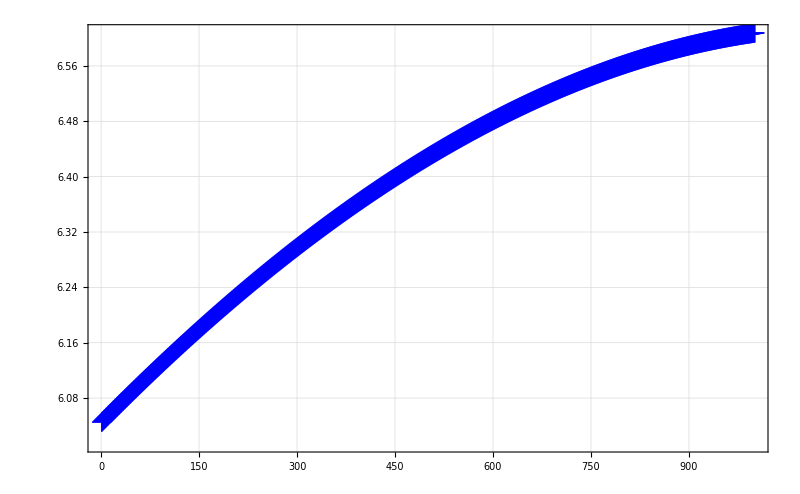

```mathematica
Texplot[steps, ϕlist[[;;, 6]], 800, "\\text{Discretisation step}", "c_3~\\text{coordinate}"]
```

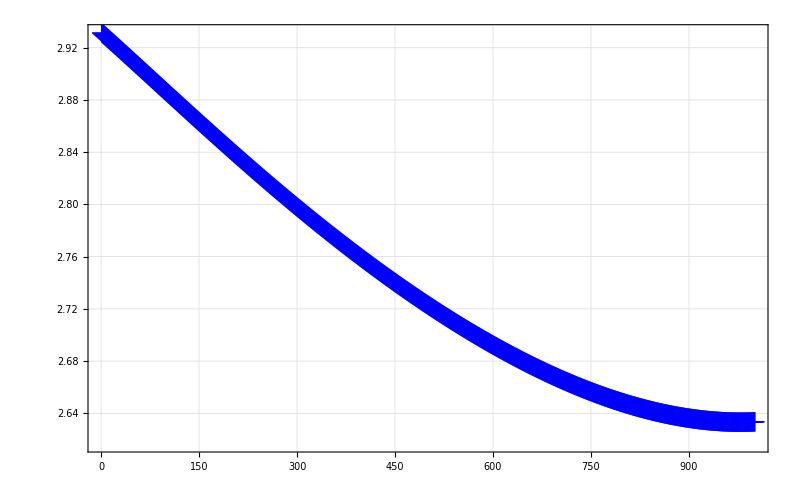

```mathematica
Inner[Rule, vars, ϕlist[[-2]], List]
```

{e1→-3.00718,e2→-0.39633,e3→0.514958,x→2.63347,y→6.49506,z→6.60757}

```mathematica
ϕlist//Length
```

1001

```mathematica
rinter//Length
```

1001

```mathematica
(*Order of the error in the constraint equations*)
```

```mathematica
e1table= Table[Max[Abs[cη@@Join[ϕlist[[ii]], rinter[[ii]]]]], {ii, Length[ϕlist]}];
```

```mathematica
Max[e1table]
```

9.70886×10^-11

```mathematica
ambrule
```

{e3→1.711,e2→0.5425,e1→-3.3553,x→2.93,y→4.07,z→6.045}

```mathematica
paperval = {e1-> −3.3553981637732204646, e2-> 0.5425359168641715099, e3-> +1.7110227662077546889, x-> +2.9313331749199504570, y-> +4.0768903590846968732, z-> +6.0451905744644536057};
```

```mathematica
cη@@Join[vars/.paperval, {ρ1, ρ2, ρ3}/.cablelendata]
```

{1.98952×10^-13,2.27374×10^-13,-3.41061×10^-13,-1.15961×10^-11,-1.59162×10^-11,2.54659×10^-11}

```mathematica
cη@@Join[test, {ρ1, ρ2, ρ3}/.cablelendata]
```

{-5.68434×10^-14,2.27374×10^-13,2.84217×10^-13,8.86757×10^-11,5.72982×10^-11,7.07701×10^-12}

```mathematica
(*Visualisation*)
```

```mathematica
A1
```

{0,0,0}

```mathematica
ϕlist[[2]][[4;;]]
```

{2.93088,4.07896,6.04615}

```mathematica
(B1+B2+B3+X)/4/.sol/.numdata2
```

{2.80293,6.51853,6.20976}

```mathematica
ϕlist//Dimensions
```

{1001,6}

```mathematica
B1list = Table[B1/.Inner[Rule, vars, ϕlist[[u]], List]/.numdata2,{u, 1, Length[ϕlist]}];
B2list = Table[B2/.Inner[Rule, vars, ϕlist[[u]], List]/.numdata2,{u, 1, Length[ϕlist]}];
B3list = Table[B3/.Inner[Rule, vars, ϕlist[[u]], List]/.numdata2,{u, 1, Length[ϕlist]}];
```

```mathematica
centerlist = (B1list+B2list+B3list+ϕlist[[;;,4;;]])/4;
```

```mathematica
sol = Inner[Rule, vars, ϕlist[[1]], List];
(*cables = Show[Graphics3D[{Thick, Red, Line[{A1, B1}]}, Boxed->False], Graphics3D[{Thick, Green, Line[{A2, B2}]}, Boxed->False], Graphics3D[{Thick, Blue,Line[{A3, B3}]}, Boxed->False]]/.numdata/.sol;*)
cables = Show[Graphics3D[{Thick, Black, Line[{A1, B1}]}, Boxed->False], Graphics3D[{Thick, Black, Line[{A2, B2}]}, Boxed->False], Graphics3D[{Thick, Black,Line[{A3, B3}]}, Boxed->False]]/.numdata/.sol;
base = Graphics3D[{Thick, Gray, Opacity[0.7], Triangle[{A1, A2, A3}/.numdata2]}, Boxed->False];
tet = Graphics3D[{Opacity[0.4], Thick, Blue, Tetrahedron[Join[{B1, B2, B3, X}/.sol/.numdata2, {ϕlist[[1]][[4;;]]}]]}, Boxed->False];
winches = Graphics3D[{Red, Sphere[{A1, A2, A3}, 0.5]} , Boxed->False]/.numdata2;
fixtures = Graphics3D[{Green, Sphere[{B1, B2, B3}, 0.2]} , Boxed->False]/.sol/.numdata2;
(*pts = Table[Graphics3D[{Red, Sphere[ϕlist[[i]][[4;;]],  0.05]}, Boxed->False], {i, 1, u}];*)
(*pts2 = Table[Graphics3D[{Red, Sphere[centerlist[[i]],  0.05]}], {i, 1, u}];*)
Show[cables, base, tet, winches, fixtures, Axes->False,AxesOrigin->Automatic, AxesLabel-> {"x","y","z"},ImageSize->{800,600}, ViewAngle->0.2564917866864384,ViewCenter->{0.5,0.5,0.5},ViewMatrix->Automatic,ViewPoint->{-5.257159306798439,0.9060886946712579,-1.0724236586347513},ViewProjection->Automatic,ViewRange->All,ViewVector->Automatic,ViewVertical->{-0.24793061691158666,0.05462901510467381,-0.9672363102709355}]
```

-Graphics3D-

```mathematica
Manipulate[
sol = Inner[Rule, vars, ϕlist[[u]], List];
(*cables = Show[Graphics3D[{Thick, Red, Line[{A1, B1}]}, Boxed->False], Graphics3D[{Thick, Green, Line[{A2, B2}]}, Boxed->False], Graphics3D[{Thick, Blue,Line[{A3, B3}]}, Boxed->False]]/.numdata/.sol;*)
cables = Show[Graphics3D[{Thick, Black, Line[{A1, B1}]}, Boxed->False], Graphics3D[{Thick, Black, Line[{A2, B2}]}, Boxed->False], Graphics3D[{Thick, Black,Line[{A3, B3}]}, Boxed->False]]/.numdata/.sol;
base = Graphics3D[{Thick, Gray, Opacity[0.7], Triangle[{A1, A2, A3}/.numdata2]}, Boxed->False];
tet = Graphics3D[{Opacity[0.4], Thick, Blue, Tetrahedron[Join[{B1, B2, B3, X}/.sol/.numdata2, {ϕlist[[u]][[4;;]]}]]}, Boxed->False];
winches = Graphics3D[{Red, Sphere[{A1, A2, A3}, 0.5]} , Boxed->False]/.numdata2;
fixtures = Graphics3D[{Green, Sphere[{B1, B2, B3}, 0.2]} , Boxed->False]/.sol/.numdata2;
(*pts = Table[Graphics3D[{Red, Sphere[ϕlist[[i]][[4;;]],  0.05]}, Boxed->False], {i, 1, u}];*)
pts2 = Table[Graphics3D[{Red, Sphere[centerlist[[i]],  0.05], Boxed->False}], {i, 1, u}];
(*Show[pts2, base, cables, tet, winches, fixtures, Axes->False,AxesOrigin->Automatic,AxesLabel-> {"x","y","z"},ImageSize->{800,600}, ViewAngle->0.2564917866864384,ViewCenter->{0.5,0.5,0.5},ViewMatrix->Automatic,ViewPoint->{-5.257159306798439,0.9060886946712579,-1.0724236586347513},ViewProjection->Automatic,ViewRange->All,ViewVector->Automatic,ViewVertical->{-0.24793061691158666,0.05462901510467381,-0.9672363102709355}]*)
Show[base,tet, fixtures, Axes->False,AxesOrigin->Automatic,AxesLabel-> {"x","y","z"},ImageSize->{800,600}, ViewAngle->0.2564917866864384,ViewCenter->{0.5,0.5,0.5},ViewPoint->{-5.257159306798439,0.9060886946712579,-1.0724236586347513},ViewVertical->{-0.24793061691158666,0.05462901510467381,-0.9672363102709355}, Boxed->False],
{u, 1, Length[ϕlist],1},ContentSize->{1000, 1000}
]
```

### Import of the Multiplication matrix from Maple

```mathematica
Me3=ToExpression[Import["Me3f.mpl"]];
```

Import::nffil: File Me3f.mpl not found during Import.

```mathematica
Dimensions[Me3]
```

{156,156}

```mathematica
Me3[[156,156]]
```

-(50671048642432902146786377527979829718274273732236957010055448629559867904759818955282818476055785677251762381253015529499195433169342942883885686509905460399171265603640713203232000296456638738936413294938707461890348159678085956332988125925379077320172073051248742184235650965950945606393667586881651294146824446404281487431857819708726744443624224956712248970467481418303975143800945541621324230267212602413489858630871734549866359035579381421096480056684178913016533024041959333552827603/10943681707036645052958241043214864840882673781719572641948388209667374705877813831880129616488688624806774544412237075147449535048746098336732503850525200014244225670682985400515632936403412117982621717892780786499535007805965534592151795816976910812087961576657635638544718799998566409635190302853528994646991510760534432007973770940768862606100184471686299132434739203325773731041244244086170451840508838963960917469228270319366001260784379231578578885375902207231598885365256371001373560)

```mathematica
Me3n=N[Me3]
```

{1}
 |  |  |  |

```mathematica
Me3n[[156,156]]
```

-4.63016

### Computation of the eigenvalues and eigenvectors of the Multiplication matrix:

```mathematica
Timing[{vals,vecs}=Eigensystem[N[Me3n,100]]]
```

{0.015625,{{2.51404+3.28227 ⅈ,2.51404-3.28227 ⅈ,2.34955+3.18047 ⅈ,2.34955-3.18047 ⅈ,3.26852+1.05166 ⅈ,3.26852-1.05166 ⅈ,145,-0.155029-0.224967 ⅈ,-0.255793+0.0800726 ⅈ,-0.255793-0.0800726 ⅈ,0.12737+0.186597 ⅈ,0.12737-0.186597 ⅈ},{{1},154,{1}}}}
 |  |  |  |

```mathematica
solall=ConstantArray[0,Length[vals]];
Do[solall[[ii]]=(vecs[[ii]]/(vecs[[ii]][[1]]))[[2;;7]],{ii,1,Length[vals]}]
```

```mathematica
valsnew={};
vecsnew={};
```

```mathematica
Do[If[Abs[Im[vals[[ii]]]]<10^-12,{valsnew,vecsnew}={Union[valsnew,{vals[[ii]]}],Union[vecsnew,{vecs[[ii]]}]}],{ii,1,156}]
```

```mathematica
valsnew
```

{-3.04369+0. ⅈ,-1.61306+0. ⅈ,-1.24796+0. ⅈ,-1.2106+0. ⅈ,-1.0066+0. ⅈ,-0.471928+0. ⅈ,0.526298+0. ⅈ,0.569622+0. ⅈ,0.965555+0. ⅈ,1.71102+0. ⅈ}

```mathematica
solr=ConstantArray[0,Length[valsnew]];
```

```mathematica
Do[solr[[ii]]=(vecsnew[[ii]]/(vecsnew[[ii]][[1]]))[[2;;7]],{ii,1,Length[valsnew]}]
```

```mathematica
solr;
```

```mathematica
posevec={e3,e2,e1,x,y,z};
```

```mathematica
solrrule=Inner[Rule,posevec,Transpose[solr],List];
```

```mathematica
solallrule=Inner[Rule,posevec,Transpose[solall],List];
```

```mathematica
sol2={x->2.5977352480361477511,y-> 3.8457865212868645040,z->-4.8661048045758031135 ,e1-> -2.6616890629909497781,e2->0.4160373487571940226,e3->0.9655548628886102991};
```

```mathematica
solrrule
```

{{e3→0.526298+0. ⅈ,e2→-0.0996113+0. ⅈ,e1→0.684445+0. ⅈ,x→2.84019+0. ⅈ,y→4.81333+0. ⅈ,z→-4.45347+0. ⅈ},{e3→-1.2106+0. ⅈ,e2→-0.487719+0. ⅈ,e1→-0.54835+0. ⅈ,x→1.81593+0. ⅈ,y→4.30222+0. ⅈ,z→5.55164+0. ⅈ},{e3→-1.24796+0. ⅈ,e2→2.59031+0. ⅈ,e1→-0.504474+0. ⅈ,x→3.52313+0. ⅈ,y→5.53202+0. ⅈ,z→5.26268+0. ⅈ},{e3→-1.61306+0. ⅈ,e2→-0.889198+0. ⅈ,e1→-0.325255+0. ⅈ,x→2.57607+0. ⅈ,y→4.39245+0. ⅈ,z→-6.75275+0. ⅈ},{e3→-0.471928+0. ⅈ,e2→-5.90417+0. ⅈ,e1→-4.22203+0. ⅈ,x→1.68046+0. ⅈ,y→3.5743+0. ⅈ,z→5.56056+0. ⅈ},{e3→-3.04369+0. ⅈ,e2→7.36708+0. ⅈ,e1→-2.52913+0. ⅈ,x→4.37572+0. ⅈ,y→5.85227+0. ⅈ,z→-4.00104+0. ⅈ},{e3→1.71102+0. ⅈ,e2→0.542536+0. ⅈ,e1→-3.3554+0. ⅈ,x→2.93133+0. ⅈ,y→4.07689+0. ⅈ,z→6.04519+0. ⅈ},{e3→-1.0066+0. ⅈ,e2→-1.27313+0. ⅈ,e1→-1.16585+0. ⅈ,x→1.39926+0. ⅈ,y→3.27949+0. ⅈ,z→5.53128+0. ⅈ},{e3→0.965555+0. ⅈ,e2→0.416038+0. ⅈ,e1→-2.66169+0. ⅈ,x→2.59773+0. ⅈ,y→3.84579+0. ⅈ,z→-4.86611+0. ⅈ},{e3→0.569622+0. ⅈ,e2→-0.145506+0. ⅈ,e1→0.543433+0. ⅈ,x→3.0241+0. ⅈ,y→4.73097+0. ⅈ,z→3.30191+0. ⅈ}}

```mathematica
Re[solr]
```

{{0.526298,-0.0996113,0.684445,2.84019,4.81333,-4.45347},{-1.2106,-0.487719,-0.54835,1.81593,4.30222,5.55164},{-1.24796,2.59031,-0.504474,3.52313,5.53202,5.26268},{-1.61306,-0.889198,-0.325255,2.57607,4.39245,-6.75275},{-0.471928,-5.90417,-4.22203,1.68046,3.5743,5.56056},{-3.04369,7.36708,-2.52913,4.37572,5.85227,-4.00104},{1.71102,0.542536,-3.3554,2.93133,4.07689,6.04519},{-1.0066,-1.27313,-1.16585,1.39926,3.27949,5.53128},{0.965555,0.416038,-2.66169,2.59773,3.84579,-4.86611},{0.569622,-0.145506,0.543433,3.0241,4.73097,3.30191}}

### Residue Computation for the solutions obtained

```mathematica
maxerror=ConstantArray[0,Length[valsnew]];
```

```mathematica
maxerrorall=ConstantArray[0,Length[vals]];
```

```mathematica
Do[maxerror[[ii]]=Abs[(Simplify[{n1,n2,n3}/.numdata])/.solrrule[[ii]]],{ii,1,Length[valsnew]}]
Do[maxerrorall[[ii]]=Abs[Simplify[{q1,q2,q3}]/.numdata/.solallrule[[ii]]],{ii,1,Length[vals]}]
```

```mathematica
maxerror[[7]]
```

{1.1417×10^-7,6.73921×10^-7,9.17539×10^-7}

```mathematica
maxerrorall[[7]]
```

{2.67633×10^-6,9.64687×10^-6,0.0000159781}

```mathematica
Abs[{q1n,q2n,q3n,p1n,p2n,p3n,p4n,p5n,p6n,p7n,p8n,p9n,p10n,p11n}/.solrrule[[10]]]
```

{0.000209495,2.94521×10^-6,0.0000154681,0.0000526401,0.00011998,0.000170064,0.00106979,0.0000294786,8.5432×10^-6,0.000393961,8.72597×10^-7,0.000175718,9.37477×10^-7,0.0000356399}

### Stability analysis:

```mathematica
{τ1,τ2,τ3}=Inverse[(Join[Transpose[{s1/ρ1}],Transpose[{s2/ρ2}],Transpose[{s3/ρ3}],2])].(QQ*KK);
```

```mathematica
tau=ConstantArray[0,Length[valsnew]];
```

```mathematica
Do[tau[[ii]]=(Re[{τ1,τ2,τ3}]/.numdata/.QQ-> 10)/.solrrule[[ii]],{ii,1,Length[valsnew]}]
```

```mathematica
{tau[[1]],tau[[2]],tau[[3]],tau[[4]],tau[[5]],tau[[6]],tau[[7]],tau[[8]],tau[[9]],tau[[10]]}
```

{{-6.00965,-7.60755,-9.52989},{5.45902,3.25456,5.49956},{2.88639,7.86816,9.12427},{-4.60909,-4.11535,-5.65302},{6.84324,3.05134,6.14352},{-1.40426,-9.301,-9.8332},{5.26131,5.11432,5.81265},{6.75887,2.50871,4.86404},{-5.70723,-4.84838,-5.59092},{5.89927,7.82791,9.56383}}

```mathematica
vectoskew[nn_?VectorQ]:=Module[{nntilda},
nntilda={{0,-nn[[3]],nn[[2]]},{nn[[3]],0,-nn[[1]]},{-nn[[2]],nn[[1]],0}};
Return[nntilda];
];
```

```mathematica
r1n=r1/.numdata/.solrrule[[1]]
```

{0.673105+0. ⅈ,0.521961+0. ⅈ,0.523914+0. ⅈ}

```mathematica
vectoskew[r1n]//MatrixForm
```

(0 | -0.523914+0. ⅈ | 0.521961+0. ⅈ
0.523914+0. ⅈ | 0 | -0.673105+0. ⅈ
-0.521961+0. ⅈ | 0.673105+0. ⅈ | 0)

```mathematica
Hp[i_]:=Module[{cons,mat11,mat12,mat21,mat22,mat},
cons=(ToExpression["τ"<>ToString[i]]/ToExpression["ρ"<>ToString[i]]);
mat11=IdentityMatrix[3];
mat12=-vectoskew[ToExpression["r"<>ToString[i]]];
mat21=-mat12;
mat22=(1/2)*(mat21.( vectoskew[X])−(mat21). (vectoskew[ToExpression["A"<>ToString[i]]])+(vectoskew[X]).mat21−(vectoskew[ToExpression["A"<>ToString[i]]]).mat21);
mat=Join[Join[mat11,mat12,2],Join[mat21,mat22,2]];
Return[mat];
]
```

```mathematica
Hpf=Hp[1]+Hp[2]+Hp[3];
```

```mathematica
Dimensions[Npn]
```

{3,6}

```mathematica
Jp=Transpose[Join[(Join[Transpose[{s1}],Transpose[{s2}],Transpose[{s3}],2]),(Join[Transpose[{Cross[r1,s1]}],Transpose[{Cross[r2,s2]}],Transpose[{Cross[r3,s3]}],2])]];
```

```mathematica
Jpn=Rationalize[(Jp/.numdata)/.solrrule[[10]],0];
Npn=NullSpace[Jpn];
Hpfn=((Npn.Hpf.Transpose[Npn])/.numdata)/.solrrule[[10]];NegativeSemidefiniteMatrixQ[Hpfn]
```

True

```mathematica
tau[[1]]
```

{5.26131+0. ⅈ,5.11432+0. ⅈ,5.81265+0. ⅈ}

### Equilibrium configurations with non-negative tension in all cables:

```mathematica
tet=ConstantArray[0,10];
tri=ConstantArray[0,10];
l1=ConstantArray[0,10];
l2=ConstantArray[0,10];
l3=ConstantArray[0,10];
Do[tet[[ii]]=Tetrahedron[{B1,B2,B3,X}/.numdata/.solrrule[[ii]]],{ii,1,10}]
Do[tri[[ii]]=Triangle[{A1,A2,A3}/.numdata/.solrrule[[ii]]],{ii,1,10}]

Do[l1[[ii]]=Line[{A1,B1}/.numdata/.solrrule[[ii]]],{ii,1,10}]
Do[l2[[ii]]=Line[{A2,B2}/.numdata/.solrrule[[ii]]],{ii,1,10}]
Do[l3[[ii]]=Line[{A3,B3}/.numdata/.solrrule[[ii]]],{ii,1,10}]
```

```mathematica
plot=ConstantArray[0,10];
Do[plot[[ii]]=Show[Graphics3D[{tri[[ii]],tet[[ii]],l1[[ii]],l2[[ii]],l3[[ii]]}],Axes->True,AxesOrigin->Automatic,AxesLabel-> {"x","y","z"},ViewPoint->{-2.7,1.9,-0.8},ViewVertical->{0.5,-0.35,-1.7},ImageSize->{800,600}],{ii,1,10}]
```

```mathematica
{plot[[2]],tau[[2]]}
```

{-Graphics3D-,{5.45902+0. ⅈ,3.25456+0. ⅈ,5.49956+0. ⅈ}}

```mathematica
{plot[[3]],tau[[3]]}
```

{-Graphics3D-,{2.88639+0. ⅈ,7.86816+0. ⅈ,9.12427+0. ⅈ}}

```mathematica
{plot[[5]],tau[[5]]}
```

{-Graphics3D-,{6.84324+0. ⅈ,3.05134+0. ⅈ,6.14352+0. ⅈ}}

```mathematica
{plot[[7]],tau[[7]]}
```

{-Graphics3D-,{5.26131+0. ⅈ,5.11432+0. ⅈ,5.81265+0. ⅈ}}

```mathematica
{plot[[8]],tau[[8]]}
```

{-Graphics3D-,{6.75887+0. ⅈ,2.50871+0. ⅈ,4.86404+0. ⅈ}}

```mathematica
{plot[[10]],tau[[10]]}
```

{-Graphics3D-,{5.89927+0. ⅈ,7.82791+0. ⅈ,9.56383+0. ⅈ}}